```mathematica
Web Based Tutorial for ME 8390

Theoretical Solutions for Phase Change Problems
By Xiaoqing Zhang
Spring Semester  2007
```

Introduction

In this web based tutorial, we will show different kinds of theoretical solutions for the phase change problems. They are under different assumptions: steady state, quasi steady state and exact  transient state.

For the phase change problem, the governing equations are:
  
  (1) Planar Coordinate System:
  
       frozen phase:
                      k_f  (∂^2 T_f)/(∂ r^2)=ρc_f   (∂ T_f)/(∂ t)
                      
     unfrozen phase:
                   k_u  (∂^2 T_u)/(∂ r^2)+m_b c_b(T_0-T_u)=ρc_u   (∂ T_u)/(∂ t)
                   
     boundary conditions:
                  T_f=T_s                                                           at r=r_0
                           T_f=T_pc=T                                                 at r=s(t)
                      k_f(∂ T_f)/(∂ r)=k_u(∂ T_u)/(∂ r)+ρL  (∂ s(t))/(∂ t)                             at r=s(t)
                           T→T_0                                                                                as r→∞
                             
  (2) Cylindrical Coordinate System:
  
       frozen phase:
                  k_f/r  (∂( r(∂T_f)/(∂ r)))/(∂ r)=ρc_f   (∂ T_f)/(∂ t)

     unfrozen phase:
                  k_u/r  (∂( r(∂T_u)/(∂ r)))/(∂ r)+m_b c_b(T_0-T_u)=ρc_u   (∂ T_u)/(∂ t)
                  
     boundary conditions:
                  T_f=T_s                                                           at r=r_0
                           T_f=T_pc=T                                                 at r=s(t)
                      k_f(∂ T_f)/(∂ r)=k_u(∂ T_u)/(∂ r)+ρL  (∂ s(t))/(∂ t)                             at r=s(t)
                           T→T_0                                                                                as r→∞
                           
  (3) Spherical Coordinate System:
  
       frozen phase:
                  k_f/r^2  (∂( r^2(∂T_f)/(∂ r)))/(∂ r)=ρc_f   (∂ T_f)/(∂ t)
                  
     unfrozen phase:
                  k_u/r^2  (∂( r^2(∂T_u)/(∂ r)))/(∂ r)+m_b c_b(T_0-T_u)=ρc_u   (∂ T_u)/(∂ t)
                  
     boundary conditions:
                  T_f=T_s                                                           at r=r_0
                           T_f=T_pc=T                                                 at r=s(t)
                      k_f(∂ T_f)/(∂ r)=k_u(∂ T_u)/(∂ r)+ρL  (∂ s(t))/(∂ t)                             at r=s(t)
                           T→T_0                                                                                as r→∞
   
   In order to simplify the analysis, Cooper and Trezek introduced the nondimensional group, shown as below:
   
   Nondimensional Parameters:
   
                   θ_f= (T_f-T_0)/(T_s-T_0),   β = (m_b c_b r_0^2)/k_u,   θ = (T-T_0)/(T_s-T_0)
                   
                                     ϕ = - k_f/k_u θ^*,   θ^* =(T_pc-T_0)/(T_pc-T_0),   θ_pc=(T_pc-T_0)/(T_s-T_0)
                                     
                                    R = r/r_o,    r^*=s/r_0,      τ=(k_u(T_0-T_pc)t)/ρLr_0^2
                                   

Part One: Steady state

In this part, the temperature distribution and the growth of iceball will be given under the assumption of steady state. These solutions are from Cooper and Trezek, 1970.  For the steady state condition, the ice front location will indicate the maximum iceball size possible for the particular situation.
The solutions to the equations above under the steady state assumption are shown under different coordinate systems. In order to show the temperature profile throught the whole region, here we assume that  ϕ =2, β =0.1 and θ_pc = 0.4.
    
(1) Planar Coordinate System
    
         The solutions of the governing equations are shown as below:

x^*=|1-ϕ/(√β)|

θ_f=(θ_pc-1)/(x^*-1)*x+(x^*-θ_pc)/(x^*-1)

θ_u=θ_pc*e^(-√β*(x-x^*))

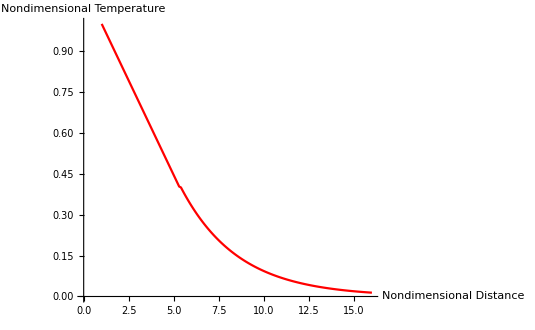

```mathematica
ϕ=2;
β=0.1;
Subscript[θ, pc]=0.4;
SuperStar[x]=Abs[1-ϕ/(√β)];
Subscript[θ, fp]=(Subscript[θ, pc]-1)/(SuperStar[x]-1)*x+(SuperStar[x]-Subscript[θ, pc])/(SuperStar[x]-1);
Subscript[θ, up]=Subscript[θ, pc]*Exp[-√β*(x-SuperStar[x])];

data1=Table[Subscript[θ, fp],{x,1,SuperStar[x],0.1}];
data2=Table[Subscript[θ, up],{x,SuperStar[x],16,0.1}];
R=Table[x,{x,1,16,0.1}];
list11={R,Join[data1,data2]};
list1=Transpose[list11];
plot1=ListPlot[list1, 
PlotStyle-> {Hue[1]}, 
Joined->True,
AxesLabel->{"Nondimensional Distance","Nondimensional Temperature"}]
Clear[list11,data1,data2,R,x]
```

(2) Cylindrical Coordinate System

The solutions of the governing equations are shown as below:

θ_f=(θ_pc-1)*ln[r]/ln[r^*]+1

 θ_u=θ_pc*(K_0(√β*r))/(K_0(√β*r^*))

and r^* is the root of the equation:

√β*r^* *(K_1(√β*r^*))/(K_0(√β*r^*))*ln[r^*]==ϕ

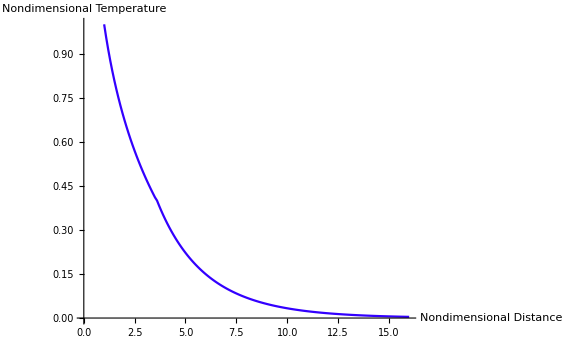

```mathematica
ϕ=2;
β=0.1;
Subscript[θ, pc]=0.4;
solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
SuperStar[r]=%;
Subscript[θ, fc]=(Subscript[θ, pc]-1)*Log[r]/Log[SuperStar[r]]+1;
Subscript[θ, uc]=Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*SuperStar[r]];

data1=Table[Subscript[θ, fc],{r,1,SuperStar[r],0.1}];
data2=Table[Subscript[θ, uc],{r,SuperStar[r],16,0.1}];
R=Table[x,{x,1,16,0.1}];
list22={R,Join[data1,data2]};
list2=Transpose[list22];
plot1=ListPlot[list2, 
PlotStyle-> {Hue[0.7]}, 
Joined->True,
AxesLabel->{"Nondimensional Distance","Nondimensional Temperature"}]
Clear[list22,data1,data2,R,x,y]
```

(3) Spherical Coordinate System

R^*=(√β-1)/(2 √β)+√((√β-1)^2/(4β)+(1+ϕ)/(√β))

 θ_f=(θ_pc-1)*R^*/(1-R^*)*(1-R)/R+1

 θ_u=θ_pc*R^*/R*e^(-√β*(R-R^*))

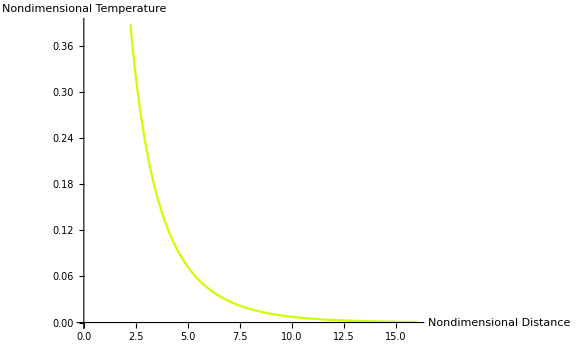

```mathematica
ϕ=2;
β=0.1;
Subscript[θ, pc]=0.4;
SuperStar[R]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];
Subscript[θ, fs]=(Subscript[θ, pc]-1)*SuperStar[R]/(1-SuperStar[R])*(1-R)/R+1;
Subscript[θ, us]=Subscript[θ, pc]*SuperStar[R]/R*Exp[-√β*(R-SuperStar[R])];

data1=Table[Subscript[θ, fs],{R,1,SuperStar[R],0.1}];
data2=Table[Subscript[θ, us],{R,SuperStar[R],16,0.1}];
R=Table[x,{x,1,16,0.1}];
list33={R,Join[data1,data2]};
list3=Transpose[list33];
plot1=ListPlot[list3, 
PlotStyle-> {Hue[0.2]}, 
Joined->True,
AxesLabel->{"Nondimensional Distance","Nondimensional Temperature"}]
Clear[list33,data1,data2,R,x,y]
```

```mathematica
(4) Comparison of the nondimensional temperature profiles for the planar, cylindrical and spherical systems
```

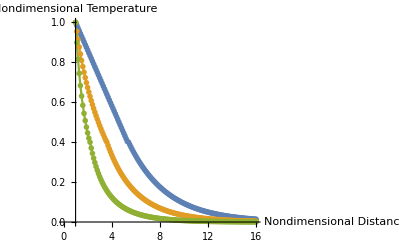

```mathematica
(*Needs["Graphics`MultipleListPlot`"]*)
ListPlot[{list1,list2,list3},
Joined->True,PlotLegend->{"Plane","Cylinder","Sphere"},LegendPosition->{0.6,0},LegendSize->{0.4,0.3},AxesOrigin->{1,0},PlotMarkers->{{Hue[1],4},{Hue[0.7],4},{Hue[0.2],4}},
(*PlotStyle->{Hue[1],Hue[0.7],Hue[0.2]},
PlotMarkers->{Hue[1],Hue[0.7],Hue[0.2]},
PlotLegends->{"Plane","Cylinder","Sphere"},LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
LegendSize->{0.5,0.35},
AxesOrigin->{1,0},*)
AxesLabel->{"Nondimensional Distance","Nondimensional Temperature"}]
```

From the figure above, we can see the temperature profiles for planar, cylindrical, and spherical cryoprobes. Here we assume the nondimensional probe temperature ϕ = 2, nondimensional phase-change temperature θ_pc= 0.4, and blood flow parameter β =2.

In the following sections, we'll show the effects of  ϕ and  β on the growth of iceball.

(5) Effect of blood flow and  probe surface temperature on the growth of the iceball

Here, we will show the effect of ϕ and  β on the growth of the iceball (θ_pc=0.4 ).

```mathematica
(*
Needs["Graphics`MultipleListPlot`"];*)
Clear[x11,x12,ϕ15]
Subscript[θ, pc]=0.4;
x11[ϕ15_]:=Abs[1-ϕ15/(√Subscript[β, 15])]/.Subscript[β, 15]->0.1;
x12[ϕ15_]=Abs[1-ϕ15/(√Subscript[β, 15])]/.Subscript[β, 15]->1;
data1=Table[{ϕ15-0.632455532033676,x11[ϕ15]},{ϕ15,0,15,0.5}];
data4=Table[{ϕ15-2,x12},{ϕ15,0,15,0.5}];
SuperStar[Subscript[R, 11]]=(√Subscript[β, 15]-1)/(2 √Subscript[β, 15])+Sqrt[(√Subscript[β, 15]-1)^2/(4 Subscript[β, 15])+(1+ϕ15)/(√Subscript[β, 15])]/.Subscript[β, 15]->0.1;
SuperStar[Subscript[R, 12]]=(√Subscript[β, 15]-1)/(2 √Subscript[β, 15])+Sqrt[(√Subscript[β, 15]-1)^2/(4 Subscript[β, 15])+(1+ϕ15)/(√Subscript[β, 15])]/.Subscript[β, 15]->1;
data3=Table[{ϕ15,SuperStar[Subscript[R, 11]]},{ϕ15,0,15,0.5}];
data6=Table[{ϕ15,SuperStar[Subscript[R, 12]]},{ϕ15,0,15,0.5}];

Subscript[β, 11]=0.1;
data2=Table[{Subscript[ϕ, 11],y/.FindRoot[√Subscript[β, 11]*y*(BesselK[1,√Subscript[β, 11]*y]/BesselK[0,√Subscript[β, 11]*y])*Log[y]==Subscript[ϕ, 11],{y,1}]},{Subscript[ϕ, 11],0,15,0.5}];
Subscript[β, 12]=1;
data5=Table[{Subscript[ϕ, 12],y/.FindRoot[√Subscript[β, 12]*y*(BesselK[1,√Subscript[β, 12]*y]/BesselK[0,√Subscript[β, 12]*y])*Log[y]==Subscript[ϕ, 12],{y,1}]},{Subscript[ϕ, 12],0,15,0.5}];
```

```mathematica
ListPlot[{data1,data2,data3,data4,data5,data6},PlotRange->{{0,15},{1,13}},PlotLegend->{"Plane, β=0.1","Cylinder, β=0.1","Sphere, β=0.1","Plane, β=1","Cylinder, β=1","Sphere, β=1"},
Joined->True,LegendPosition->{1,0},LegendSize->Automatic,
(*PlotStyle->{{Hue[1],4},{Hue[0.7],4},{Hue[0.2],4},{Hue[1],4},{Hue[0.7],4},{Hue[0.2],4}},
PlotLegend->{"Plane, β=0.1","Cylinder, β=0.1","Sphere, β=0.1","Plane, β=1","Cylinder, β=1","Sphere, β=1"},*)
(*PlotRange->{{0,15},{1,13}},
AxesOrigin->{0,1},
LegendShadow->{0.04,-0.04},
LegendSize->{0.7,0.35},*)
AxesLabel->{"ϕ","Nondimensional Ice Front"}]
Clear[data1,data2,data3,data4,data5,data6]
```

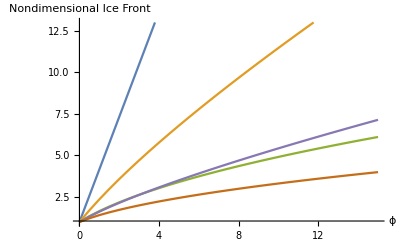

From the figure, we can see clearly the effect  of ϕ and  β on the growth of the iceball. For the same value of probe surface temperature, the size of iceball is bigger with smaller blood flow parameter. And for the same value of blood flow parameter, the size of iceball is bigger with lower probe surface temperature.

Part Two: Quasi Steady state

In this part, the temperature distribution and the growth of iceball will be given under the assumption of quasi steady state. These solutions are from Cooper and Trezek, 1971.  For the quasi  steady  state condition, these solutions include the contribution of blood flow and metabolic heat generation and do not require the tissue to be initially at its phase change temperature. Heat capacity effects in both the frozen and unfrozen regions have been neglected in the development of these solutions. 

(1) Spherical Coordinate System

The approximate solutions are obtained under the assumption that [kc_f(T_0-T_pc)]/k_fL and [c(T_0-T_pc)]/L are small. Then the nondimensional governing equations become:

(∂(R^2(∂θ_f)/(∂R)))/(∂R)=0

   1/R^2(∂(R^2(∂θ_u)/(∂R)))/(∂R)-βθ_u=0

And the solutions of the temperature profiles are:

θ_f=(θ_pc-1)*R^*/(1-R^*)*(1-R)/R+1

    θ_u=θ_pc*R^*/R*e^(-√β*(R-R^*))

The temperature profiles are transient in nature by virtue of the time dependence of R^*.  The location of the ice front is given by:

τ=(∫_1)^(R^*)(μ(1-μ)dμ)/(√β μ^2+(1-√β)μ-(1+ϕ))

This integral can be evaluated exactly to give:

τ=1/(2 a^2)ln{(a R^(*2)+(1-a)R^*+c)/(1+c)}+(1-a(1+2c))/(2 a^2 b)ln{(a(2 R^*-1+b+1))/(a(2 R^*-1-b+1))*(a-b+1)/(a+b+1)}-(R^*-1)/a

where

a=√β; b=√((1-a)^2-4ac); c=-(1+ϕ)

In order to show the temperature distribution and history, here we assume that ϕ=2, β=0.1 and θ_pc=0.4.

```mathematica
β=0.1;
Subscript[θ, pc]=0.4;

Subscript[θ, 2fs]=(Subscript[θ, pc]-1)*SuperStar[R]/(1-SuperStar[R])*(1-R)/R+1;
Subscript[θ, 2us]=Subscript[θ, pc]*SuperStar[R]/R*Exp[-√β*(R-SuperStar[R])];
```

First, we will show the temperature distribution throughout the region at different time points.

```mathematica
(*Needs["Graphics`MultipleListPlot`"]*)
a=√β;
c=-(1+ϕ);
b=√((1-a)^2-4a*c);
τ=1/(2*a^2)*Log[(a*(x)^2+(1-a)*x+c)/(1+c)]+(1-a*(1+2*c))/(2 a^2*b)Log[(a*(2*x-1)+b+1)/(a*(2*x-1)-b+1)*(a-b+1)/(a+b+1)]-(x-1)/a;

IceFront=Table[{τ,x},{x,4,20,4}];
data1=Table[(Subscript[θ, pc]-1)*4/(1-4)*(1-R)/R+1,{R,1,4}];
data2=Table[Subscript[θ, pc]*4/R*Exp[-√β*(R-4)],{R,5,25}];
data3=Table[(Subscript[θ, pc]-1)*8/(1-8)*(1-R)/R+1,{R,1,8}];
data4=Table[Subscript[θ, pc]*8/R*Exp[-√β*(R-8)],{R,9,25}];
data5=Table[(Subscript[θ, pc]-1)*12/(1-12)*(1-R)/R+1,{R,1,12}];
data6=Table[Subscript[θ, pc]*12/R*Exp[-√β*(R-12)],{R,13,25}];
data7=Table[(Subscript[θ, pc]-1)*16/(1-16)*(1-R)/R+1,{R,1,16}];
data8=Table[Subscript[θ, pc]*16/R*Exp[-√β*(R-16)],{R,17,25}];
data9=Table[(Subscript[θ, pc]-1)*20/(1-20)*(1-R)/R+1,{R,1,20}];
data10=Table[Subscript[θ, pc]*20/R*Exp[-√β*(R-20)],{R,21,25}];
R=Table[x,{x,1,25}];
list11={R,Join[data1,data2]};
list22={R,Join[data3,data4]};
list33={R,Join[data5,data6]};
list44={R,Join[data7,data8]};
list55={R,Join[data9,data10]};
list1=Transpose[list11];
list2=Transpose[list22];
list3=Transpose[list33];
list4=Transpose[list44];
list5=Transpose[list55];
```

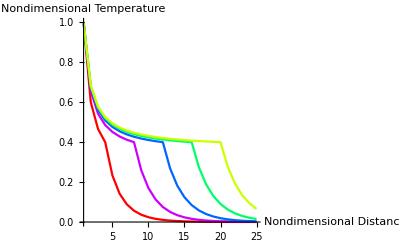

```mathematica
ListPlot[{list1,list2,list3,list4,list5},
Joined->True,PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},PlotRange->All,PlotLegend->{"R^* = 4","R^* = 8","R^* = 12","R^* = 16","R^* = 20"},LegendPosition->{0.6,0},AxesOrigin->{1,0},LegendShadow->{0.04,-0.04},LegendSize->{0.35,0.35},
(*PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
SymbolShape->{PlotSymbol[Triangle],PlotSymbol[Box],PlotSymbol[Star],PlotSymbol[Diamond],PlotSymbol[Diamond],PlotSymbol[Triangle]},
PlotRange->All,
AxesOrigin->{1,0},
PlotLegend->{"R^* = 4","R^* = 8","R^* = 12","R^* = 16","R^* = 20"},
SymbolStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
LegendSize->{0.35,0.35},*)
AxesLabel->{"Nondimensional Distance","Nondimensional Temperature"}]
Clear[data1,data2,data3,data4,data5,data6,data7,data8,data9,data10,list11,list22,list33,list44,list55,list1,list2,list3,list4,list5,τ,x,IceFront];
```

Then, we will show the temperature history at different distance from the probe.

```mathematica
(*Needs["Graphics`MultipleListPlot`"];*)

ϕ=50;
β=0.1;
Subscript[θ, pc]=0.4;

Subscript[R, ss]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];

a=√β;
c=-(1+ϕ);
b=√((1-a)^2-4a*c);
τ=1/(2*a^2)*Log[(a*(x)^2+(1-a)*x+c)/(1+c)]+(1-a*(1+2*c))/(2 a^2*b)Log[(a*(2*x-1)+b+1)/(a*(2*x-1)-b+1)*(a-b+1)/(a+b+1)]-(x-1)/a;

IceFront=Table[τ,{x,1,11,0.1}];

data1=Table[(Subscript[θ, pc]-1)*SuperStar[R]/(1-SuperStar[R])*(1-2)/2+1,{SuperStar[R],2.1,11,0.1}];
data2=Table[Subscript[θ, pc]*SuperStar[R]/2*Exp[-√β*(2-SuperStar[R])],{SuperStar[R],1,2,0.1}];
data3=Table[(Subscript[θ, pc]-1)*SuperStar[R]/(1-SuperStar[R])*(1-4)/4+1,{SuperStar[R],4.1,11,0.1}];
data4=Table[Subscript[θ, pc]*SuperStar[R]/4*Exp[-√β*(4-SuperStar[R])],{SuperStar[R],1,4,0.1}];
data5=Table[(Subscript[θ, pc]-1)*SuperStar[R]/(1-SuperStar[R])*(1-6)/6+1,{SuperStar[R],6.1,11,0.1}];
data6=Table[Subscript[θ, pc]*SuperStar[R]/6*Exp[-√β*(6-SuperStar[R])],{SuperStar[R],1,6,0.1}];
data7=Table[(Subscript[θ, pc]-1)*SuperStar[R]/(1-SuperStar[R])*(1-8)/8+1,{SuperStar[R],8.1,11,0.1}];
data8=Table[Subscript[θ, pc]*SuperStar[R]/8*Exp[-√β*(8-SuperStar[R])],{SuperStar[R],1,8,0.1}];
data9=Table[(Subscript[θ, pc]-1)*SuperStar[R]/(1-SuperStar[R])*(1-10)/10+1,{SuperStar[R],10.1,11,0.1}];
data10=Table[Subscript[θ, pc]*SuperStar[R]/10*Exp[-√β*(10-SuperStar[R])],{SuperStar[R],1,10,0.1}];

list11={IceFront,Join[data2,data1]};
list22={IceFront,Join[data4,data3]};
list33={IceFront,Join[data6,data5]};
list44={IceFront,Join[data8,data7]};
list55={IceFront,Join[data10,data9]};
list1=Transpose[list11];
list2=Transpose[list22];
list3=Transpose[list33];
list4=Transpose[list44];
list5=Transpose[list55];
```

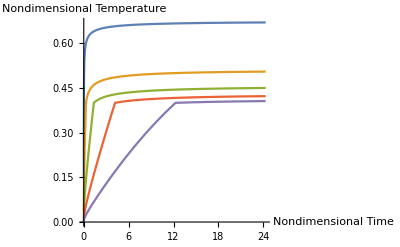

```mathematica
plot12=ListPlot[{list1,list2,list3,list4,list5},
Joined->True,AxesLabel->{"Nondimensional Time","Nondimensional Temperature"},PlotLegend->{"R = 2","R = 4","R = 6","R = 8","R = 10"},LegendPosition->{1,0},LegendShadow->{0.04,-0.04},LegendSize->{0.35,0.35}
(*PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
SymbolShape->{PlotSymbol[Triangle],PlotSymbol[Box],PlotSymbol[Star],PlotSymbol[Diamond],PlotSymbol[Triangle]},
PlotRange->All,
AxesLabel->{"Nondimensional Time","Nondimensional Temperature"},
PlotLegend->{"R = 2","R = 4","R = 6","R = 8","R = 10"},
SymbolStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
LegendSize->{0.35,0.35}*)]
Clear[data1,data2,data3,data4,data5,data6,data7,data8,data9,data10,list11,list22,list33,list44,list55,list1,list2,list3,list4,list5,τ,x,IceFront];
```

(2) Cylindrical Coordinate System

Under the assumption of quasi steady state, the nondimensional governing equation become:

(∂(R(∂θ_f)/(∂R)))/(∂R)=0

   1/R(∂(R(∂θ_u)/(∂R)))/(∂R)-βθ_u=0

And the solutions of the temperature profiles are:

θ_f=(θ_pc-1)*ln[r]/ln[r^*]+1

   θ_u=θ_pc*(K_0(√β*r))/(K_0(√β*r^*))

And the time-dependent ice front location is given by:

τ=(∫_1)^(R^*)(K_0(√β μ)μln(μ)dμ)/(ϕK_0(√β μ)-√β K_1(√β μ)μln(μ))

First, we will show the temperature distribution throughout the region at different time points.

```mathematica
(*Needs["Graphics`MultipleListPlot`"];*)
β=0.1;
Subscript[θ, pc]=0.4;
Subscript[θ, fc]=(Subscript[θ, pc]-1)*Log[r]/Log[SuperStar[r]]+1;
Subscript[θ, uc]=Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*SuperStar[r]];

data1=Table[(Subscript[θ, pc]-1)*Log[r]/Log[4]+1,{r,1,4}];
data2=Table[Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*4],{r,5,25}];
data3=Table[(Subscript[θ, pc]-1)*Log[r]/Log[8]+1,{r,1,8}];
data4=Table[Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*8],{r,9,25}];
data5=Table[(Subscript[θ, pc]-1)*Log[r]/Log[12]+1,{r,1,12}];
data6=Table[Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*12],{r,13,25}];
data7=Table[(Subscript[θ, pc]-1)*Log[r]/Log[16]+1,{r,1,16}];
data8=Table[Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*16],{r,17,25}];
data9=Table[(Subscript[θ, pc]-1)*Log[r]/Log[20]+1,{r,1,20}];
data10=Table[Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*20],{r,21,25}];
R=Table[x,{x,1,25}];
list11={R,Join[data1,data2]};
list22={R,Join[data3,data4]};
list33={R,Join[data5,data6]};
list44={R,Join[data7,data8]};
list55={R,Join[data9,data10]};
list1=Transpose[list11];
list2=Transpose[list22];
list3=Transpose[list33];
list4=Transpose[list44];
list5=Transpose[list55];
```

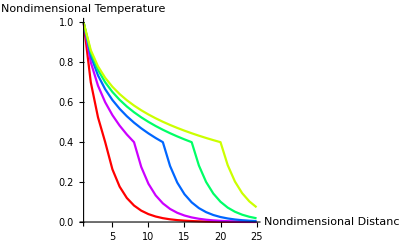

```mathematica
ListPlot[{list1,list2,list3,list4,list5},
Joined->True,
PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
PlotRange->All,
AxesOrigin->{1,0},
PlotLegend->{"R^* = 4","R^* = 8","R^* = 12","R^* = 16","R^* = 20"},
LegendPosition->{0.4,0},
LegendShadow->{0.04,-0.04},
LegendSize->{0.5,0.35},
AxesLabel->{"Nondimensional Distance","Nondimensional Temperature"}]
Clear[data1,data2,data3,data4,data5,data6,data7,data8,data9,data10,list11,list22,list33,list44,list55,list1,list2,list3,list4,list5,τ,x,IceFront];
```

Then, we will show the temperature history at different distance from the probe.

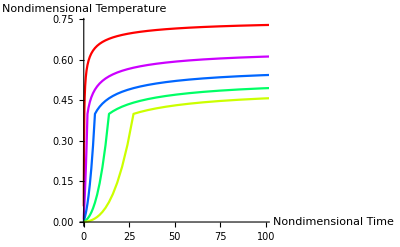

```mathematica
(*Needs["Graphics`MultipleListPlot`"];
*)
ϕ=50;
β=0.1;
Subscript[θ, pc]=0.4;
Subscript[θ, fc]=(Subscript[θ, pc]-1)*Log[r]/Log[SuperStar[r]]+1;
Subscript[θ, uc]=Subscript[θ, pc]*BesselK[0,√β*r]/BesselK[0,√β*SuperStar[r]];

a=BesselK[0,√β*μ];
b=BesselK[1,√β*μ];
c=(a*μ*Log[μ])/(ϕ*a-√β*b*μ*Log[μ]);


solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
Subscript[r, ss]=%;

IceFront=Table[NIntegrate[c,{μ,1,x}],{x,1,40}];

data1=Table[(Subscript[θ, pc]-1)*Log[5]/Log[SuperStar[r]]+1,{SuperStar[r],6,40}];
data2=Table[Subscript[θ, pc]*BesselK[0,√β*5]/BesselK[0,√β*SuperStar[r]],{SuperStar[r],1,5}];
data3=Table[(Subscript[θ, pc]-1)*Log[10]/Log[SuperStar[r]]+1,{SuperStar[r],11,40}];
data4=Table[Subscript[θ, pc]*BesselK[0,√β*10]/BesselK[0,√β*SuperStar[r]],{SuperStar[r],1,10}];
data5=Table[(Subscript[θ, pc]-1)*Log[15]/Log[SuperStar[r]]+1,{SuperStar[r],16,40}];
data6=Table[Subscript[θ, pc]*BesselK[0,√β*15]/BesselK[0,√β*SuperStar[r]],{SuperStar[r],1,15}];
data7=Table[(Subscript[θ, pc]-1)*Log[20]/Log[SuperStar[r]]+1,{SuperStar[r],21,40}];
data8=Table[Subscript[θ, pc]*BesselK[0,√β*20]/BesselK[0,√β*SuperStar[r]],{SuperStar[r],1,20}];
data9=Table[(Subscript[θ, pc]-1)*Log[25]/Log[SuperStar[r]]+1,{SuperStar[r],26,40}];
data10=Table[Subscript[θ, pc]*BesselK[0,√β*25]/BesselK[0,√β*SuperStar[r]],{SuperStar[r],1,25}];
list11={IceFront,Join[data2,data1]};
list22={IceFront,Join[data4,data3]};
list33={IceFront,Join[data6,data5]};
list44={IceFront,Join[data8,data7]};
list55={IceFront,Join[data10,data9]};
list1=Transpose[list11];
list2=Transpose[list22];
list3=Transpose[list33];
list4=Transpose[list44];
list5=Transpose[list55];
ListPlot[{list1,list2,list3,list4,list5},
Joined->True,
PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
(*SymbolShape->{PlotSymbol[Triangle],PlotSymbol[Box],PlotSymbol[Star],PlotSymbol[Diamond],PlotSymbol[Triangle]},*)
PlotRange->{{0,100},All},
AxesLabel->{"Nondimensional Time","Nondimensional Temperature"},
PlotLegend->{"R = 5","R = 10","R = 15","R = 20","R = 25"},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
(*SymbolStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},*)
LegendSize->{0.35,0.35}]
Clear[data1,data2,data3,data4,data5,data6,data7,data8,data9,data10,list11,list22,list33,list44,list55,list1,list2,list3,list4,list5,τ,x,IceFront];
```

(3) Effect of probe surface temperature and blood flow on the rate of the iceball growth 

In this section, we will show how the parameter ϕ and β influence the rate of the iceball growth.

Here, we assume  β=0.1,

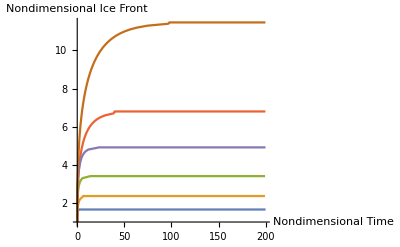

```mathematica
(*Needs["Graphics`MultipleListPlot`"]*)

β=0.1;

ϕ=1;

solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
Subscript[r, ss]=%;

Subscript[R, ss]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];

a1=√β;
c1=-(1+ϕ);
b1=√((1-a1)^2-4a1*c1);
t1=1/(2*(a1)^2)*Log[(a1*(x)^2+(1-a1)*x+c1)/(1+c1)]+(1-a1*(1+2*c1))/(2*(a1)^2*b1)Log[(a1*(2*x-1)+b1+1)/(a1*(2*x-1)-b1+1)*(a1-b1+1)/(a1+b1+1)]-(x-1)/a1;

IceFront11=Table[{t1,x},{x,1,Subscript[R, ss],0.1}];
l1=200-Floor[IceFront11[[-1,1]]]-1;
IceFront1={Join[IceFront11[[All,1]],Table[t,{t,IceFront11[[-1,1]]+1,200}]],Join[IceFront11[[All,2]],Table[Subscript[R, ss],{l1}]]};
list1=Transpose[IceFront1];

a2=BesselK[0,√β*μ];
b2=BesselK[1,√β*μ];
c2=(a2*μ*Log[μ])/(ϕ*a2-√β*b2*μ*Log[μ]);

IceFront21=Table[{NIntegrate[c2,{μ,1,x}],x},{x,1,Subscript[r, ss],0.1}];
l2=200-Floor[IceFront21[[-1,1]]]-1;
IceFront2={Join[IceFront21[[All,1]],Table[t,{t,IceFront21[[-1,1]]+1,200}]],Join[IceFront21[[All,2]],Table[Subscript[r, ss],{l2}]]};
list2=Transpose[IceFront2];
Clear[IceFront11,IceFront1,IceFront21,IceFront2];


ϕ=5;

solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
Subscript[r, ss]=%;

Subscript[R, ss]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];

a1=√β;
c1=-(1+ϕ);
b1=√((1-a1)^2-4a1*c1);
t1=1/(2*(a1)^2)*Log[(a1*(x)^2+(1-a1)*x+c1)/(1+c1)]+(1-a1*(1+2*c1))/(2*(a1)^2*b1)Log[(a1*(2*x-1)+b1+1)/(a1*(2*x-1)-b1+1)*(a1-b1+1)/(a1+b1+1)]-(x-1)/a1;

IceFront11=Table[{t1,x},{x,1,Subscript[R, ss],0.1}];
l1=200-Floor[IceFront11[[-1,1]]]-1;
IceFront1={Join[IceFront11[[All,1]],Table[t,{t,IceFront11[[-1,1]]+1,200}]],Join[IceFront11[[All,2]],Table[Subscript[R, ss],{l1}]]};
list3=Transpose[IceFront1];

a2=BesselK[0,√β*μ];
b2=BesselK[1,√β*μ];
c2=(a2*μ*Log[μ])/(ϕ*a2-√β*b2*μ*Log[μ]);

IceFront21=Table[{NIntegrate[c2,{μ,1,x}],x},{x,1,Subscript[r, ss],0.1}];
l2=200-Floor[IceFront21[[-1,1]]]-1;
IceFront2={Join[IceFront21[[All,1]],Table[t,{t,IceFront21[[-1,1]]+1,200}]],Join[IceFront21[[All,2]],Table[Subscript[r, ss],{l2}]]};
list4=Transpose[IceFront2];
Clear[IceFront11,IceFront1,IceFront21,IceFront2];

ϕ=10;

solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
Subscript[r, ss]=%;

Subscript[R, ss]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];
Rtemp=Subscript[R, ss]-0.01;

a1=√β;
c1=-(1+ϕ);
b1=√((1-a1)^2-4a1*c1);
t1=1/(2*(a1)^2)*Log[(a1*(x)^2+(1-a1)*x+c1)/(1+c1)]+(1-a1*(1+2*c1))/(2*(a1)^2*b1)Log[(a1*(2*x-1)+b1+1)/(a1*(2*x-1)-b1+1)*(a1-b1+1)/(a1+b1+1)]-(x-1)/a1;

IceFront11=Table[{t1,x},{x,1,Subscript[R, ss],0.1}];
l1=200-Floor[IceFront11[[-1,1]]]-1;
IceFront1={Join[IceFront11[[All,1]],Table[t,{t,IceFront11[[-1,1]]+1,200}]],Join[IceFront11[[All,2]],Table[Subscript[R, ss],{l1}]]};
list5=Transpose[IceFront1];

a2=BesselK[0,√β*μ];
b2=BesselK[1,√β*μ];
c2=(a2*μ*Log[μ])/(ϕ*a2-√β*b2*μ*Log[μ]);

IceFront21=Table[{NIntegrate[c2,{μ,1,x}],x},{x,1,Subscript[r, ss],0.1}];
l2=200-Floor[IceFront21[[-1,1]]]-1;
IceFront2={Join[IceFront21[[All,1]],Table[t,{t,IceFront21[[-1,1]]+1,200}]],Join[IceFront21[[All,2]],Table[Subscript[r, ss],{l2}]]};
list6=Transpose[IceFront2];
Clear[IceFront11,IceFront1,IceFront21,IceFront2];

ListPlot[{list1,list2,list3,list4,list5,list6},
Joined->True,
(*PlotStyle->{Hue[1],Hue[1],Hue[0.7],Hue[0.7],Hue[0.2],Hue[0.2]},*)
(*PlotMarkers->{Triangle,Box,Triangle,Box,4,Triangle,Box},*)
PlotRange->All,
AxesLabel->{"Nondimensional Time","Nondimensional Ice Front"},
PlotLegend->{"Sphere, ϕ=1","Cylinder, ϕ=1","Sphere, ϕ=5","Cylinder, ϕ=5","Sphere, ϕ=10","Cylinder, ϕ=10"},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
LegendLabel->"β=0.1",
AxesOrigin->{0,1},
LegendSize->{0.5,0.35}]
```

Then, we assume  β=1,

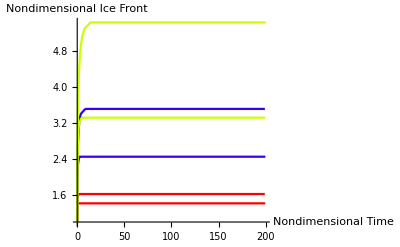

```mathematica
(*Needs["Graphics`MultipleListPlot`"];*)

β=1;

ϕ=1;

solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
Subscript[r, ss]=%;

Subscript[R, ss]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];

a1=√β;
c1=-(1+ϕ);
b1=√((1-a1)^2-4a1*c1);
t1=1/(2*(a1)^2)*Log[(a1*(x)^2+(1-a1)*x+c1)/(1+c1)]+(1-a1*(1+2*c1))/(2*(a1)^2*b1)Log[(a1*(2*x-1)+b1+1)/(a1*(2*x-1)-b1+1)*(a1-b1+1)/(a1+b1+1)]-(x-1)/a1;

IceFront11=Table[{t1,x},{x,1,Subscript[R, ss],0.1}];
l1=200-Floor[IceFront11[[-1,1]]]-1;
IceFront1={Join[IceFront11[[All,1]],Table[t,{t,IceFront11[[-1,1]]+1,200}]],Join[IceFront11[[All,2]],Table[Subscript[R, ss],{l1}]]};
list1=Transpose[IceFront1];

a2=BesselK[0,√β*μ];
b2=BesselK[1,√β*μ];
c2=(a2*μ*Log[μ])/(ϕ*a2-√β*b2*μ*Log[μ]);

IceFront21=Table[{NIntegrate[c2,{μ,1,x}],x},{x,1,Subscript[r, ss],0.1}];
l2=200-Floor[IceFront21[[-1,1]]]-1;
IceFront2={Join[IceFront21[[All,1]],Table[t,{t,IceFront21[[-1,1]]+1,200}]],Join[IceFront21[[All,2]],Table[Subscript[r, ss],{l2}]]};
list2=Transpose[IceFront2];
Clear[IceFront11,IceFront1,IceFront21,IceFront2];


ϕ=5;

solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
Subscript[r, ss]=%;

Subscript[R, ss]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];

a1=√β;
c1=-(1+ϕ);
b1=√((1-a1)^2-4a1*c1);
t1=1/(2*(a1)^2)*Log[(a1*(x)^2+(1-a1)*x+c1)/(1+c1)]+(1-a1*(1+2*c1))/(2*(a1)^2*b1)Log[(a1*(2*x-1)+b1+1)/(a1*(2*x-1)-b1+1)*(a1-b1+1)/(a1+b1+1)]-(x-1)/a1;

IceFront11=Table[{t1,x},{x,1,Subscript[R, ss],0.1}];
l1=200-Floor[IceFront11[[-1,1]]]-1;
IceFront1={Join[IceFront11[[All,1]],Table[t,{t,IceFront11[[-1,1]]+1,200}]],Join[IceFront11[[All,2]],Table[Subscript[R, ss],{l1}]]};
list3=Transpose[IceFront1];

a2=BesselK[0,√β*μ];
b2=BesselK[1,√β*μ];
c2=(a2*μ*Log[μ])/(ϕ*a2-√β*b2*μ*Log[μ]);

IceFront21=Table[{NIntegrate[c2,{μ,1,x}],x},{x,1,Subscript[r, ss],0.1}];
l2=200-Floor[IceFront21[[-1,1]]]-1;
IceFront2={Join[IceFront21[[All,1]],Table[t,{t,IceFront21[[-1,1]]+1,200}]],Join[IceFront21[[All,2]],Table[Subscript[r, ss],{l2}]]};
list4=Transpose[IceFront2];
Clear[IceFront11,IceFront1,IceFront21,IceFront2];

ϕ=10;

solutions=FindRoot[√β*y*(BesselK[1,√β*y]/BesselK[0,√β*y])*Log[y]==ϕ,{y,1}];
y/.solutions;
Subscript[r, ss]=%;

Subscript[R, ss]=(√β-1)/(2 √β)+Sqrt[(√β-1)^2/(4β)+(1+ϕ)/(√β)];
Rtemp=Subscript[R, ss]-0.01;

a1=√β;
c1=-(1+ϕ);
b1=√((1-a1)^2-4a1*c1);
t1=1/(2*(a1)^2)*Log[(a1*(x)^2+(1-a1)*x+c1)/(1+c1)]+(1-a1*(1+2*c1))/(2*(a1)^2*b1)Log[(a1*(2*x-1)+b1+1)/(a1*(2*x-1)-b1+1)*(a1-b1+1)/(a1+b1+1)]-(x-1)/a1;

IceFront11=Table[{t1,x},{x,1,Subscript[R, ss],0.1}];
l1=200-Floor[IceFront11[[-1,1]]]-1;
IceFront1={Join[IceFront11[[All,1]],Table[t,{t,IceFront11[[-1,1]]+1,200}]],Join[IceFront11[[All,2]],Table[Subscript[R, ss],{l1}]]};
list5=Transpose[IceFront1];

a2=BesselK[0,√β*μ];
b2=BesselK[1,√β*μ];
c2=(a2*μ*Log[μ])/(ϕ*a2-√β*b2*μ*Log[μ]);

IceFront21=Table[{NIntegrate[c2,{μ,1,x}],x},{x,1,Subscript[r, ss],0.1}];
l2=200-Floor[IceFront21[[-1,1]]]-1;
IceFront2={Join[IceFront21[[All,1]],Table[t,{t,IceFront21[[-1,1]]+1,200}]],Join[IceFront21[[All,2]],Table[Subscript[r, ss],{l2}]]};
list6=Transpose[IceFront2];
Clear[IceFront11,IceFront1,IceFront21,IceFront2];

ListPlot[{list1,list2,list3,list4,list5,list6},
Joined->True,
PlotStyle->{Hue[1],Hue[1],Hue[0.7],Hue[0.7],Hue[0.2],Hue[0.2]},
(*PlotMarkers->{PlotMarder[Triangle],PlotSymbol[Box],PlotSymbol[Triangle],PlotSymbol[Box],PlotSymbol[Triangle],PlotSymbol[Box]},*)
PlotRange->All,
AxesLabel->{"Nondimensional Time","Nondimensional Ice Front"},
PlotLegend->{"Sphere, ϕ=1","Cylinder, ϕ=1","Sphere, ϕ=5","Cylinder, ϕ=5","Sphere, ϕ=10","Cylinder, ϕ=10"},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
LegendLabel->"β=1",
AxesOrigin->{0,1},
LegendSize->{0.5,0.35}]
Clear[list1,list2,list3,list4,list5,list6]
```

From the figures above, we can note that for a fixed value of the blood flow parameter, the time required to reach steady state is increased as the nondimensional probe surface temperature is increased. On the other hand, for a fixed probe surface temperature, the time required to reach steady state is increased as the value of the blood flow parameter is increased.

Part Three: Transient State

In this part, the exact temperature distribution and the growth of iceball will be given. These solutions are from "Heat Conduction", Ozisik. 

(1) Planar Coordinate System

The exact solution of this phase change problem is shown as Neumann's solution. We have the following transcendental equation for the determination of s(t), the location of the ice front.

(e^(-λ^2))/(erf(λ))+k_u/k_s √(α_f/α_u)(T_m-T_i)/(T_m-T_0)(e^(-λ^2(α_f/α_u)))/(erfc(λ √(α_f/α_u)))=(λL √π)/(C_ps(T_m-T_0))

And the temperature profiles are given by:

(T_f-T_0)/(T_m-T_0)=erf[√(x/(2(α_f t)))]/(erf(λ))

  (T_u-T_0)/(T_m-T_0)=erf[√(x/(2(α_u t)))]/(erf(√(λ α_f/α_u)))

the ice front s(t) is shown as:

s(t)=2λ √(α_s t)

In order to show the temperature profile and history , first we should give values to some parameters.

```mathematica
Subscript[T, 0]=-196;
Subscript[T, m]=0;
Subscript[T, i]=37;
Subscript[k, u]=0.6;
Subscript[k, f]=2.24;
Subscript[C, pf]=2093;
Subscript[C, pu]=4200;
ρ=999;
L=335000;
```

First, we'll show the temperature distribution,

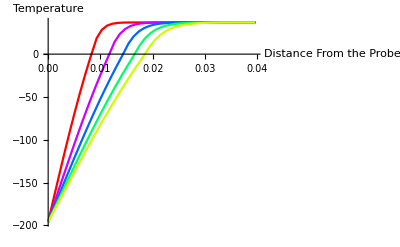

```mathematica
(*Needs["Graphics`MultipleListPlot`"];*)
Subscript[α, f]=Subscript[k, f]/(Subscript[C, pf]*ρ);
Subscript[α, u]=Subscript[k, u]/(Subscript[C, pu]*ρ);
N1=Exp[-x*x]/Erf[x];
N2=Subscript[k, u]/Subscript[k, f]*√(Subscript[α, f]/Subscript[α, u])*(Subscript[T, m]-Subscript[T, i])/(Subscript[T, m]-Subscript[T, 0])*Exp[-x*x*Subscript[α, f]/Subscript[α, u]]/Erfc[x*√(Subscript[α, f]/Subscript[α, u])];
N3=(x*L*√3.14)/(Subscript[C, pf]*(Subscript[T, m]-Subscript[T, 0]));
solutions=FindRoot[N1+N2==N3,{x,1}];
x/.solutions;
λ=%;

Subscript[T, f]=Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[r/(2*√(Subscript[α, f]*t))]/Erf[λ];
Subscript[T, u]=Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[r/(2*√(Subscript[α, u]*t))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])];
s=2*λ*√(Subscript[α, f]*t);
list1=Table[{r,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[r/(2*√(Subscript[α, f]*50))]/Erf[λ]},{r,0,2*λ*√(Subscript[α, f]*50),0.001}];
list2=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[r/(2*√(Subscript[α, u]*50))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{r,2*λ*√(Subscript[α, f]*50)+0.001,0.04,0.001}];

list3=Table[{r,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[r/(2*√(Subscript[α, f]*100))]/Erf[λ]},{r,0,2*λ*√(Subscript[α, f]*100),0.001}];
list4=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[r/(2*√(Subscript[α, u]*100))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{r,2*λ*√(Subscript[α, f]*100)+0.001,0.04,0.001}];
list5=Table[{r,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[r/(2*√(Subscript[α, f]*150))]/Erf[λ]},{r,0,2*λ*√(Subscript[α, f]*150),0.001}];
list6=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[r/(2*√(Subscript[α, u]*150))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{r,2*λ*√(Subscript[α, f]*150)+0.001,0.04,0.001}];
list7=Table[{r,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[r/(2*√(Subscript[α, f]*200))]/Erf[λ]},{r,0,2*λ*√(Subscript[α, f]*200),0.001}];
list8=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[r/(2*√(Subscript[α, u]*200))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{r,2*λ*√(Subscript[α, f]*200)+0.001,0.04,0.001}];
list9=Table[{r,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[r/(2*√(Subscript[α, f]*250))]/Erf[λ]},{r,0,2*λ*√(Subscript[α, f]*250),0.001}];
list10=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[r/(2*√(Subscript[α, u]*250))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{r,2*λ*√(Subscript[α, f]*250)+0.001,0.04,0.001}];
list11=Transpose[{Join[list1[[All,1]],list2[[All,1]]],Join[list1[[All,2]],list2[[All,2]]]}];
list22=Transpose[{Join[list3[[All,1]],list4[[All,1]]],Join[list3[[All,2]],list4[[All,2]]]}];
list33=Transpose[{Join[list5[[All,1]],list6[[All,1]]],Join[list5[[All,2]],list6[[All,2]]]}];
list44=Transpose[{Join[list7[[All,1]],list8[[All,1]]],Join[list7[[All,2]],list8[[All,2]]]}];
list55=Transpose[{Join[list9[[All,1]],list10[[All,1]]],Join[list9[[All,2]],list10[[All,2]]]}];

ListPlot[{list11,list22,list33,list44,list55},
Joined->True,
PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
PlotRange->All,
AxesLabel->{"Distance From the Probe/m","Temperature"},
PlotLegend->{"t = 50s","t = 100s","t = 150s","t = 200s","t = 250s"},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
(*SymbolStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]}*)
AxesOrigin->{0,0},
LegendSize->{0.5,0.35}]
Clear[list1,list2,list3,list4,list5,list6,list7,list8,list9,list10,list11,list22,list33,list44,list55]
```

Then, we'll show the temperature history,

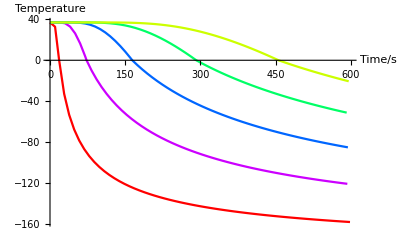

```mathematica
(*Needs["Graphics`MultipleListPlot`"];*)

Subscript[T, 0]=-196;
Subscript[T, m]=0;
Subscript[T, i]=37;
Subscript[k, u]=0.6;
Subscript[k, f]=2.24;
Subscript[C, pf]=2093;
Subscript[C, pu]=4200;
ρ=999;
L=335000;


Subscript[α, f]=Subscript[k, f]/(Subscript[C, pf]*ρ);
Subscript[α, u]=Subscript[k, u]/(Subscript[C, pu]*ρ);
N1=Exp[-x*x]/Erf[x];
N2=Subscript[k, u]/Subscript[k, f]*√(Subscript[α, f]/Subscript[α, u])*(Subscript[T, m]-Subscript[T, i])/(Subscript[T, m]-Subscript[T, 0])*Exp[-x*x*Subscript[α, f]/Subscript[α, u]]/Erfc[x*√(Subscript[α, f]/Subscript[α, u])];
N3=(x*L*√3.14)/(Subscript[C, pf]*(Subscript[T, m]-Subscript[T, 0]));
solutions=FindRoot[N1+N2==N3,{x,1}];
x/.solutions;
λ=%;


Subscript[T, f]=Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[r/(2*√(Subscript[α, f]*t))]/Erf[λ];
Subscript[T, u]=Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[r/(2*√(Subscript[α, u]*t))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])];
s=2*λ*√(Subscript[α, f]*t);
list1=Table[{t,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[0.005/(2*√(Subscript[α, f]*t))]/Erf[λ]},{t,t/.FindRoot[s==0.005,{t,1}],600,10}];
list2=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[0.005/(2*√(Subscript[α, u]*t))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{t,0.1,t/.FindRoot[s==0.005,{t,1}],10}];

list3=Table[{t,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[0.01/(2*√(Subscript[α, f]*t))]/Erf[λ]},{t,t/.FindRoot[s==0.01,{t,1}],600,10}];
list4=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[0.01/(2*√(Subscript[α, u]*t))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{t,0.1,t/.FindRoot[s==0.01,{t,1}],10}];
list5=Table[{t,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[0.015/(2*√(Subscript[α, f]*t))]/Erf[λ]},{t,t/.FindRoot[s==0.015,{t,1}],600,10}];
list6=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[0.015/(2*√(Subscript[α, u]*t))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{t,0.1,t/.FindRoot[s==0.015,{t,1}],10}];
list7=Table[{t,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[0.02/(2*√(Subscript[α, f]*t))]/Erf[λ]},{t,t/.FindRoot[s==0.02,{t,1}],600,10}];
list8=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[0.02/(2*√(Subscript[α, u]*t))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{t,0.1,t/.FindRoot[s==0.02,{t,1}],10}];
list9=Table[{t,Subscript[T, 0]+(Subscript[T, m]-Subscript[T, 0])*Erf[0.025/(2*√(Subscript[α, f]*t))]/Erf[λ]},{t,t/.FindRoot[s==0.025,{t,1}],600,10}];
list10=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*Erfc[0.025/(2*√(Subscript[α, u]*t))]/Erfc[λ*√(Subscript[α, f]/Subscript[α, u])]},{t,0.1,t/.FindRoot[s==0.025,{t,1}],10}];
list11=Transpose[{Join[list2[[All,1]],list1[[All,1]]],Join[list2[[All,2]],list1[[All,2]]]}];
list22=Transpose[{Join[list4[[All,1]],list3[[All,1]]],Join[list4[[All,2]],list3[[All,2]]]}];
list33=Transpose[{Join[list6[[All,1]],list5[[All,1]]],Join[list6[[All,2]],list5[[All,2]]]}];
list44=Transpose[{Join[list8[[All,1]],list7[[All,1]]],Join[list8[[All,2]],list7[[All,2]]]}];
list55=Transpose[{Join[list10[[All,1]],list9[[All,1]]],Join[list10[[All,2]],list9[[All,2]]]}];

ListPlot[{list11,list22,list33,list44,list55},
Joined->True,
PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
PlotRange->All,
AxesLabel->{"Time/s","Temperature"},
PlotLegend->{"r = 5mm","r = 10mm","r = 15mm","r = 20mm","r = 25mm"},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
(*SymbolStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},*)
AxesOrigin->{0,0},
LegendSize->{0.5,0.35}]
Clear[list1,list2,list3,list4,list5,list6,list7,list8,list9,list10,list11,list22,list33,list44,list55]
```

Then, we'll show the growth of the iceball

```mathematica
Subscript[T, 0]=-196;
Subscript[T, m]=0;
Subscript[T, i]=37;
Subscript[k, u]=0.6;
Subscript[k, f]=2.24;
Subscript[C, pf]=2093;
Subscript[C, pu]=4200;
ρ=999;
L=335000;


Subscript[α, f]=Subscript[k, f]/(Subscript[C, pf]*ρ);
Subscript[α, u]=Subscript[k, u]/(Subscript[C, pu]*ρ);
N1=Exp[-x*x]/Erf[x];
N2=Subscript[k, u]/Subscript[k, f]*√(Subscript[α, f]/Subscript[α, u])*(Subscript[T, m]-Subscript[T, i])/(Subscript[T, m]-Subscript[T, 0])*Exp[-x*x*Subscript[α, f]/Subscript[α, u]]/Erfc[x*√(Subscript[α, f]/Subscript[α, u])];
N3=(x*L*√3.14)/(Subscript[C, pf]*(Subscript[T, m]-Subscript[T, 0]));
solutions=FindRoot[N1+N2==N3,{x,1}];
x/.solutions;
λ=%;

s=2*λ*√(Subscript[α, f]*t);
Plot[s,{t,0,600},
AxesLabel->{"Time/s","Location of Ice Front/m"}]
```

(2) Cylindrical Coordinate System (Line Heat Source)

This is an ideal situation where we suppose that there exists a line heat sink, whose strength is Q W/m. We have the following transcendental equation for the determination of s(t), the location of the ice front:

Q/(4π)e^(-λ^2)+(k_u(T_i-T_m))/(Ei(-λ^2 α_f/α_u))e^(-λ^2 α_f/α_u)=λ^2 α_f ρL

And the temperature profiles are given by:

T_f(r,t)=T_m+Q/(4 πk_f)[Ei(-r^2/(4 α_f t))-Ei(-λ^2)] 

    T_u(r,t)=T_i-(T_i-T_m)/(Ei(-λ^2 α_f/α_u))Ei(-r^2/(4 α_u t))

the ice front s(t) is shown as:

s(t)=2λ √(α_s t)

```mathematica
Subscript[T, m]=0;
Subscript[T, i]=37;
Subscript[k, u]=0.6;
Subscript[k, f]=2.24;
Subscript[C, pf]=2093;
Subscript[C, pu]=4200;
ρ=999;
L=335000;
Q=300;

Needs["Graphics`MultipleListPlot`"];

Subscript[α, f]=Subscript[k, f]/(Subscript[C, pf]*ρ);
Subscript[α, u]=Subscript[k, u]/(Subscript[C, pu]*ρ);

N1=(Q*Exp[-x*x])/(4*3.14);
N2=(Subscript[k, u]*(Subscript[T, i]-Subscript[T, m]))/ExpIntegralEi[-x*x*Subscript[α, f]/Subscript[α, u]]*Exp[-x*x*Subscript[α, f]/Subscript[α, u]];
N3=x^2*L*ρ*Subscript[α, f];
solutions=FindRoot[N1+N2==N3,{x,1}];
x/.solutions;
λ=%;

Subscript[T, f]=Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-r^2/(4*Subscript[α, f]*t)]-ExpIntegralEi[-λ^2]);
Subscript[T, u]=Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-r^2/(4*Subscript[α, u]*t)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]];
s=2*λ*√(Subscript[α, f]*t);
list1=Table[{r,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-r^2/(4*Subscript[α, f]*50)]-ExpIntegralEi[-λ^2])},{r,0.001,2*λ*√(Subscript[α, f]*50),0.001}];
list2=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-r^2/(4*Subscript[α, u]*50)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{r,2*λ*√(Subscript[α, f]*50)+0.001,0.025,0.001}];
list3=Table[{r,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-r^2/(4*Subscript[α, f]*100)]-ExpIntegralEi[-λ^2])},{r,0.001,2*λ*√(Subscript[α, f]*100),0.001}];
list4=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-r^2/(4*Subscript[α, u]*100)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{r,2*λ*√(Subscript[α, f]*100)+0.001,0.025,0.001}];
list5=Table[{r,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-r^2/(4*Subscript[α, f]*150)]-ExpIntegralEi[-λ^2])},{r,0.001,2*λ*√(Subscript[α, f]*150),0.001}];
list6=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-r^2/(4*Subscript[α, u]*150)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{r,2*λ*√(Subscript[α, f]*150)+0.001,0.025,0.001}];
list7=Table[{r,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-r^2/(4*Subscript[α, f]*200)]-ExpIntegralEi[-λ^2])},{r,0.001,2*λ*√(Subscript[α, f]*200),0.001}];
list8=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-r^2/(4*Subscript[α, u]*200)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{r,2*λ*√(Subscript[α, f]*200)+0.001,0.025,0.001}];
list9=Table[{r,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-r^2/(4*Subscript[α, f]*250)]-ExpIntegralEi[-λ^2])},{r,0.001,2*λ*√(Subscript[α, f]*250),0.001}];
list10=Table[{r,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-r^2/(4*Subscript[α, u]*250)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{r,2*λ*√(Subscript[α, f]*250)+0.001,0.025,0.001}];
list11=Transpose[{Join[list1[[All,1]],list2[[All,1]]],Join[list1[[All,2]],list2[[All,2]]]}];
list22=Transpose[{Join[list3[[All,1]],list4[[All,1]]],Join[list3[[All,2]],list4[[All,2]]]}];
list33=Transpose[{Join[list5[[All,1]],list6[[All,1]]],Join[list5[[All,2]],list6[[All,2]]]}];
list44=Transpose[{Join[list7[[All,1]],list8[[All,1]]],Join[list7[[All,2]],list8[[All,2]]]}];
list55=Transpose[{Join[list9[[All,1]],list10[[All,1]]],Join[list9[[All,2]],list10[[All,2]]]}];

MultipleListPlot[list11,list22,list33,list44,list55,
PlotJoined->True,
PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
PlotRange->All,
AxesLabel->{"Distance From the Probe/m","Temperature"},
PlotLegend->{"t = 50s","t = 100s","t = 150s","t = 200s","t = 250s"},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
SymbolStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
AxesOrigin->{0,0},
LegendSize->{0.5,0.35}];
Clear[list1,list2,list3,list4,list5,list6,list7,list8,list9,list10,list11,list22,list33,list44,list55]
```

```mathematica
Subscript[T, m]=0;
Subscript[T, i]=37;
Subscript[k, u]=0.6;
Subscript[k, f]=2.24;
Subscript[C, pf]=2093;
Subscript[C, pu]=4200;
ρ=999;
L=335000;
Q=300;

Needs["Graphics`MultipleListPlot`"];

Subscript[α, f]=Subscript[k, f]/(Subscript[C, pf]*ρ);
Subscript[α, u]=Subscript[k, u]/(Subscript[C, pu]*ρ);

N1=(Q*Exp[-x*x])/(4*3.14);
N2=(Subscript[k, u]*(Subscript[T, i]-Subscript[T, m]))/ExpIntegralEi[-x*x*Subscript[α, f]/Subscript[α, u]]*Exp[-x*x*Subscript[α, f]/Subscript[α, u]];
N3=x^2*L*ρ*Subscript[α, f];
solutions=FindRoot[N1+N2==N3,{x,1}];
x/.solutions;
λ=%;

Subscript[T, f]=Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-r^2/(4*Subscript[α, f]*t)]-ExpIntegralEi[-λ^2]);
Subscript[T, u]=Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-r^2/(4*Subscript[α, u]*t)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]];
s=2*λ*√(Subscript[α, f]*t);

list1=Table[{t,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-(0.002)^2/(4*Subscript[α, f]*t)]-ExpIntegralEi[-λ^2])},{t,t/.FindRoot[s==0.002,{t,1}],600,10}];
list2=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-(0.002)^2/(4*Subscript[α, u]*t)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{t,0.1,t/.FindRoot[s==0.002,{t,1}],10}];

list3=Table[{t,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-(0.004)^2/(4*Subscript[α, f]*t)]-ExpIntegralEi[-λ^2])},{t,t/.FindRoot[s==0.004,{t,1}],600,10}];
list4=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-(0.004)^2/(4*Subscript[α, u]*t)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{t,0.1,t/.FindRoot[s==0.004,{t,1}],10}];

list5=Table[{t,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-(0.006)^2/(4*Subscript[α, f]*t)]-ExpIntegralEi[-λ^2])},{t,t/.FindRoot[s==0.006,{t,1}],600,10}];
list6=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-(0.006)^2/(4*Subscript[α, u]*t)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{t,0.1,t/.FindRoot[s==0.006,{t,1}],10}];

list7=Table[{t,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-(0.008)^2/(4*Subscript[α, f]*t)]-ExpIntegralEi[-λ^2])},{t,t/.FindRoot[s==0.008,{t,1}],600,10}];
list8=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-(0.008)^2/(4*Subscript[α, u]*t)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{t,0.1,t/.FindRoot[s==0.008,{t,1}],10}];

list9=Table[{t,Subscript[T, m]+Q/(4*3.14*Subscript[k, f])*(ExpIntegralEi[-(0.01)^2/(4*Subscript[α, f]*t)]-ExpIntegralEi[-λ^2])},{t,t/.FindRoot[s==0.01,{t,1}],600,10}];
list10=Table[{t,Subscript[T, i]+(Subscript[T, m]-Subscript[T, i])*ExpIntegralEi[-(0.01)^2/(4*Subscript[α, u]*t)]/ExpIntegralEi[-λ^2*Subscript[α, f]/Subscript[α, u]]},{t,0.1,t/.FindRoot[s==0.01,{t,1}],10}];

list11=Transpose[{Join[list2[[All,1]],list1[[All,1]]],Join[list2[[All,2]],list1[[All,2]]]}];
list22=Transpose[{Join[list4[[All,1]],list3[[All,1]]],Join[list4[[All,2]],list3[[All,2]]]}];
list33=Transpose[{Join[list6[[All,1]],list5[[All,1]]],Join[list6[[All,2]],list5[[All,2]]]}];
list44=Transpose[{Join[list8[[All,1]],list7[[All,1]]],Join[list8[[All,2]],list7[[All,2]]]}];
list55=Transpose[{Join[list10[[All,1]],list9[[All,1]]],Join[list10[[All,2]],list9[[All,2]]]}];
MultipleListPlot[list11,list22,list33,list44,list55,
PlotJoined->True,
PlotStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
PlotRange->{{0,600},All},
AxesLabel->{"Time/s","Temperature"},
PlotLegend->{"r = 2mm","r = 4mm","r = 6mm","r = 8mm","r = 10mm"},
LegendPosition->{1,0},
LegendShadow->{0.04,-0.04},
SymbolStyle->{Hue[1],Hue[0.8],Hue[0.6],Hue[0.4],Hue[0.2]},
AxesOrigin->{0,0},
LegendSize->{0.5,0.35}];
Clear[list1,list2,list3,list4,list5,list6,list7,list8,list9,list10,list11,list22,list33,list44,list55]
```

Then, we'll show the growth of the iceball

```mathematica
Subscript[T, m]=0;
Subscript[T, i]=37;
Subscript[k, u]=0.6;
Subscript[k, f]=2.24;
Subscript[C, pf]=2093;
Subscript[C, pu]=4200;
ρ=999;
L=335000;
Q=300;

Subscript[α, f]=Subscript[k, f]/(Subscript[C, pf]*ρ);
Subscript[α, u]=Subscript[k, u]/(Subscript[C, pu]*ρ);

N1=(Q*Exp[-x*x])/(4*3.14);
N2=(Subscript[k, u]*(Subscript[T, i]-Subscript[T, m]))/ExpIntegralEi[-x*x*Subscript[α, f]/Subscript[α, u]]*Exp[-x*x*Subscript[α, f]/Subscript[α, u]];
N3=x^2*L*ρ*Subscript[α, f];
solutions=FindRoot[N1+N2==N3,{x,1}];
x/.solutions;
λ=%;

s=2*λ*√(Subscript[α, f]*t);
Plot[s,{t,0,600},
AxesLabel->{"Time/s","Location of Ice Front/m"}]
```

(3) Spherical Coordinate System

This solution is from Paterson "Proc. Glasgow Math. Assoc.", 1952-53. The strength of the heat sink increases with time as Q=qt^0.5. The temperature profiles are given by:

T_u(r,t)=T_i+(C_pu(T_m-T_i))/L[1-(1/r √(α_u/α_f t)exp(-r^2/(4t)α_f/α_u)-(√π)/2 erfc(r/2 √(α_f/(α_u t))))/(1/(2λ)√(α_u/α_f)exp(-λ^2 α_f/α_u)-(√π)/2 erfc(λ √(α_f/α_u)))]

 T_f(r,t)=T_m+q/(4π){(√t)/r exp(-r^2/(4t))-1/(2λ)exp(-λ^2)+(√π)/2[erfc(r/(2 √t))-erfc(λ)]}

The radius of the sphere as a function of time is:

R_f(t)=2λ √t

where λ is the root of

q/(4π)e^(-λ^2)+4 λ^3+(2λ (C_pf(T_i-T_m))/L k_u/k_f)/(1-√((α_f π)/α_u)λ exp(λ^2 α_f/α_u)erfc(√(α_f/α_u)λ))=0

Temperature Distribution